```mathematica
(* The Base directory when working on the lab computer *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{homeComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
labelSize=18;
```

/home/karl/Dropbox/00School/research

1→3_15_17_AimingFor5e12

2→4-18-17

3→4-22-17

4→data

5→Data Before 4-1-17

6→firstRun2017

7→labBook

8→legacy

9→machineShopOrders

10→mathematicaCode

11→mathematicaRb

12→operationManuals

13→papers

14→polarization_4-18-17

15→polarization_4-4-17

16→polarization_4-6-17

17→probeLaserPower

18→pumpLaserFindingCircular_3-29_17

19→RbControlPiPrograms

20→rbsim

21→requisitions

22→wavemeterNoRb

23→wavemeterReliability_3-30-17

24→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[3]]}];
SetDirectory[rootFolder];absFileNames=FileNames["RbAbs*.dat"];
For[i=1,i<=Length[absFileNames],i++,
Print[i -> absFileNames[[i]]];]
```

1→RbAbs2017-04-22_222613.dat

2→RbAbs2017-04-22_223204.dat

3→RbAbs2017-04-22_223518.dat

4→RbAbs2017-04-22_230947.dat

5→RbAbs2017-04-22_231706.dat

6→RbAbs2017-04-23_000443.dat

7→RbAbs2017-04-23_023347.dat

8→RbAbs2017-04-23_024028.dat

9→RbAbs2017-04-23_045244.dat

RbAbs2017-04-22_222613.dat

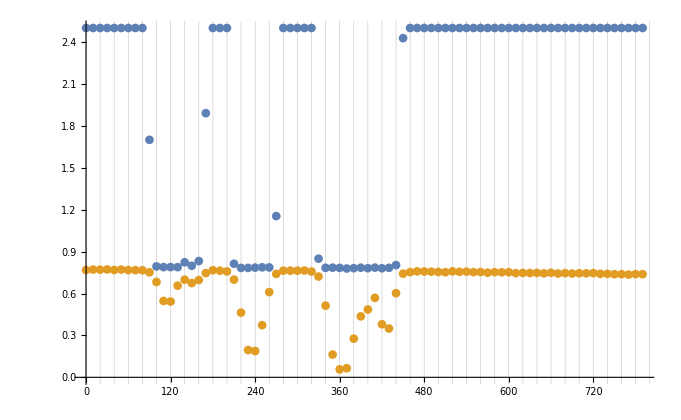

```mathematica
absFileName=absFileNames[[1]]
(*Import the absorption data*)
rbAbsorption=Import[FileNameJoin[{Directory[],absFileName}],"tsv"];
(* Drop the information from the file that isn't needed *)
rbAbsorptionRef=Drop[Take[rbAbsorption,{13,-2},{1,7}],None,{2,6}];
rbAbsorptionPro=Drop[Take[rbAbsorption,{13,-2},{1,5}],None,{2,4}];
(* Plot the data so the user can see the first minimum *)
ListPlot[{rbAbsorptionPro,rbAbsorptionRef},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None}]
```

Dataset[<>]

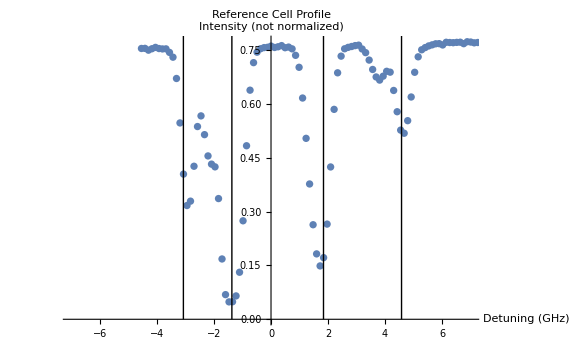

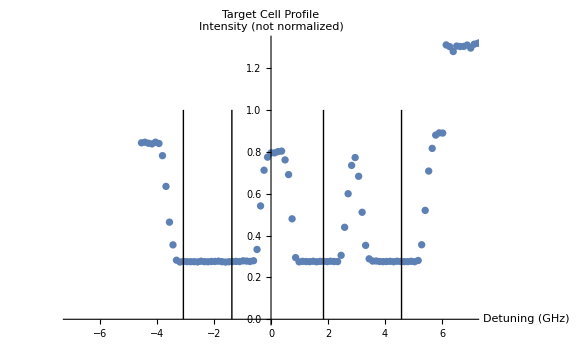

```mathematica
(*User inputs a value close to the first minimum*)
{firstTransitionValue,transitionLetter,lastTransitionLetter}={120,"D","A"};
CtoDDiff=110;
BtoCDiff=125;
AtoBDiff=72;
dt=4.576;
ct=1.84;
bt=-1.372;
at=-3.072;
transGHz={4.576,1.84,-1.372,-3.072};
aoutSteps={CtoDDiff,BtoCDiff,AtoBDiff};

(*Find the closest data point to the value chosen by the user*)
s=Nearest[Take[rbAbsorptionRef,All,1],firstTransitionValue];
(*Convert this data point to a position in the list*)

startPos=Position[Take[rbAbsorptionRef,All,1],s[[1]]][[1]][[1]];
(*Use the position in the list to find the first absorption peak's value*)
scanStepSize=Abs[(rbAbsorptionRef[[startPos]]-rbAbsorptionRef[[startPos+1]])[[1]]];
posLower=startPos-3;
posUpper=startPos+2;
transAout={0,0,0,0};
i=0;

If[transitionLetter=="D",j=1,If[transitionLetter=="C",j=2,If[transitionLetter=="B",j=3,If[transitionLetter=="A",j=4,j=5]]]];
If[lastTransitionLetter=="D",k=1,If[lastTransitionLetter=="C",k=2,If[lastTransitionLetter=="B",k=3,If[lastTransitionLetter=="A",k=4,k=5]]]];
(*Cycle through and find the remaining transisition "peaks"*)
While[And[j≤k],
peak=Min[Take[rbAbsorptionRef,{posLower,posUpper},All]];
(*Use the value of the first absorption peak to find its position in the list*)
aoutPos=Position[rbAbsorptionRef,peak][[1,1]];
(*Use the position in the list to get the Aout value located there*)
transAout[[j]]=rbAbsorptionRef[[aoutPos,1]];
(*Because the profile is consistent,we can guess at where the next min.will be*)
If[j<4,aoutPrev=transAout[[j]];aoutStep=aoutSteps[[j]];
aoutNextApprox=aoutPrev+aoutStep;
s=Nearest[Take[rbAbsorptionRef,All,1],aoutNextApprox];
posLower=aoutPos+Floor[aoutStep/scanStepSize]-2*Floor[10/scanStepSize];
posUpper=aoutPos+Floor[aoutStep/scanStepSize]+2*Floor[10/scanStepSize];];
j++;];

(*Remove the transistions that we don't have from the list so that we can estimate a linear function relating the data points that we do have*)
aoutConvData=Dataset[Transpose[{transAout,transGHz}]];
aoutConvData=aoutConvData[Select[Abs[#[[1]]]>0&]]
aoutConvData=Normal[aoutConvData];


(*Make a linear fit on the data to obtain an AOUT->GHz Conversion*)
lm2=LinearModelFit[aoutConvData,x,x];
aoutConv=lm2["BestFitParameters"][[2]];
aoutIntercept=lm2["BestFitParameters"][[1]];
rbAbsorptionRefT=Transpose[rbAbsorptionRef];
rbAbsorptionRefDet=Transpose[{rbAbsorptionRefT[[1]]*aoutConv +aoutIntercept,rbAbsorptionRefT[[2]]}];
transitionLines=Line[{{{transGHz[[1]],0},{transGHz[[1]],1}},{{transGHz[[2]],0},{transGHz[[2]],1}},{{transGHz[[3]],0},{transGHz[[3]],1}},{{transGHz[[4]],0},{transGHz[[4]],1}}}];
ListPlot[rbAbsorptionRefDet,PlotRange->{{-7,7},All},ImageSize->Large,
PlotLabel->"Reference Cell Profile",AxesLabel->{"Detuning (GHz)","Intensity (not normalized)"},LabelStyle->labelSize,Epilog->Style[transitionLines,Dotted]]

rbAbsorptionProT=Transpose[rbAbsorptionPro];
rbAbsorptionProDet=Transpose[{rbAbsorptionProT[[1]]*aoutConv +aoutIntercept,rbAbsorptionProT[[2]]}];
ListPlot[rbAbsorptionProDet,PlotRange->{{-7,7},All},PlotLabel-> "Target Cell Profile",AxesLabel->{"Detuning (GHz)","Intensity (not normalized)"},
LabelStyle->labelSize,Epilog->Style[transitionLines,Dotted]]
```